# Pêndulo Elástico em Coordenadas Cartesianas

## Definindo as Condições Iniciais

k - Constante Elástica da Mola = 1 N/m
m - Massa da partícula Suspensa = 1 kg
g - Aceleração da Gravidade Local = 9.81 m/s^2
l_0 - Tamanho da Mola em Repouso (sem compressão ou distensão) = 0.5 m
l - Tamanho da mola em repouso com a massa suspensa
ωs - Frequência da Mola
ωp - Frequência do Pêndulo
u -

```mathematica
k=6
m=1.2
g=9.81
l0 = 0.5
l=l0+m*g/k
ωs=Sqrt[k/m]
ωp=Sqrt[g/l]
μ=1+((k*l0)/(m*g))
```

6

1.2

9.81

0.5

2.462

2.23607

1.99614

1.25484

```mathematica
1.0509683995922527
(ωs/ωp)^2
```

1.05097

1.25484

## Escrevendo as Equações de Movimento

```mathematica
a=NDSolve[{x''[t]==(-k/m)* x[t]*((1-l0/(Sqrt[x[t]^2+y[t]^2]))),y''[t]==-g-((k/m)* y[t]*((1-l0/(Sqrt[x[t]^2+y[t]^2])))),x[0]==+1,y[0]==-5,x'[0]==y'[0]==0},{y[t],x[t]},{t,0,1000}]
```

{{y[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],x[t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}}

## Plotando a Evolução das Coordenadas em Função do Tempo

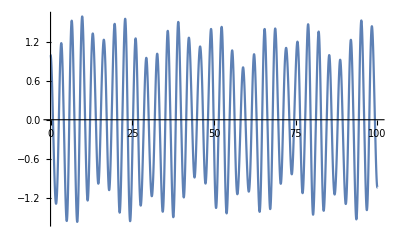

```mathematica
Plot[Evaluate[x[t]/.a],{t,0,100}]
```

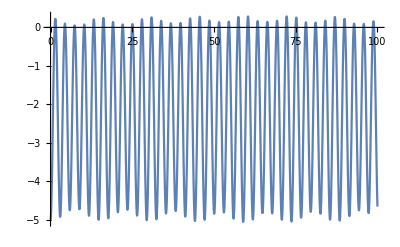

```mathematica
Plot[Evaluate[y[t]/.a],{t,0,100}]
```

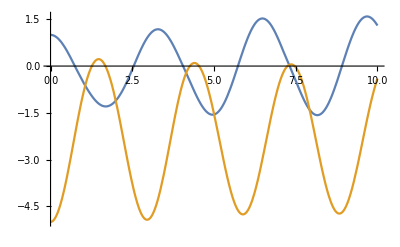

```mathematica
Plot[Evaluate[{x[t],y[t]}/.a],{t,0,10}]
```

```mathematica
PlotScale
```

PlotScale

## Mostrando a Trajetória do Pêndulo

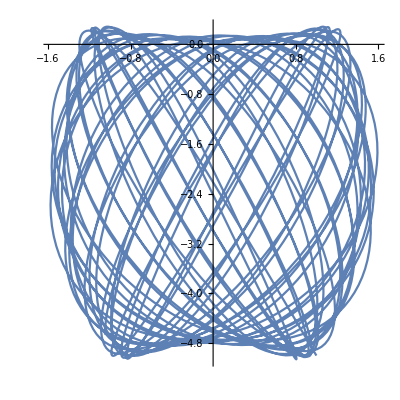

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.a],{t,0,100},AspectRatio->1]
```

```mathematica
Animate[ParametricPlot[Evaluate[{x[t],y[t]}/.a],{t,0,i},AspectRatio->1],{i,0,100,1}]
```